```mathematica
X=3 a (1-t)^2 t+3 (1-a) (1-t) t^2+t^3;
Y=3b t(1-t);
```

```mathematica
dXdt=Simplify[D[X,t]]
```

-6 (-1+t) t+3 a (1-6 t+6 t^2)

```mathematica
dYdt=Factor[D[Y,t]]
```

-3 b (-1+2 t)

```mathematica
Factor[CoefficientList[Expand[D[(x-X)^2+(y-Y)^2,{t,1}]],t]]
```

{-6 (a x+b y),6 (3 a^2+3 b^2-2 x+6 a x+2 b y),-6 (-9 a+27 a^2+9 b^2-2 x+6 a x),12 (3-22 a+39 a^2+3 b^2),-60 (-1+3 a)^2,24 (-1+3 a)^2}

```mathematica
Factor[CoefficientList[Expand[D[(x-X)^2+(y-Y)^2,{t,2}]],t]]
```

{6 (3 a^2+3 b^2-2 x+6 a x+2 b y),-12 (-9 a+27 a^2+9 b^2-2 x+6 a x),36 (3-22 a+39 a^2+3 b^2),-240 (-1+3 a)^2,120 (-1+3 a)^2}

```mathematica
CoefficientList[Expand[2(X-x)dXdt+2(Y-y)dYdt],t]
```

{-6 a x-6 b y,18 a^2+18 b^2-12 x+36 a x+12 b y,54 a-162 a^2-54 b^2+12 x-36 a x,36-264 a+468 a^2+36 b^2,-60+360 a-540 a^2,24-144 a+216 a^2}

```mathematica
Collect[D[(x-X)^2+(y-Y)^2,a],a]
Simplify[(%-18(a-1)((1-t)^2 t-(1-t) t^2)^2)/(-3( (1-t)^2 t-(1-t) t^2))]
```

2 a (-3 (1-t)^2 t+3 (1-t) t^2)^2+2 (-3 (1-t)^2 t+3 (1-t) t^2) (-3 (1-t) t^2-t^3+x)

2 (-3 t+6 t^2-4 t^3+x)

```mathematica
Simplify[D[(x-(a B31+(1-a)B32+B33))^2+(y-Y)^2,a]]
```

2 (B31-B32) (a (B31-B32)+B32+B33-x)

```mathematica
FullSimplify[Expand[D[(x-X)^2+(y-Y)^2,{t,1}]]/Expand[D[(x-X)^2+(y-Y)^2,{t,2}]]]
```

(3 a^2 (-1+t) t (-1+2 t) (1+6 (-1+t) t)+(-1+t) t (b^2 (-3+6 t)+2 (t^2 (-3+2 t)+x))-a (x+t (t (-9+4 t (11+3 t (-5+2 t)))+6 (-1+t) x))+b (-1+2 t) y)/(3 b^2 (1+6 (-1+t) t)+3 a^2 (1+6 (-1+t) t (3+10 (-1+t) t))-2 x+6 a (t (3-2 t (11+10 (-2+t) t)-2 x)+x)+2 t (t (9+10 (-2+t) t)+2 x)+2 b y)

```mathematica
Collect[Simplify[X/.t->1/2-1/2 √(1-y)],{√(1-y),y}]
```

1/2+√(1-y) (-1/2+1/4 (-1+3 a) y)

```mathematica
FullSimplify[D[1/2-1/4(2+(1-3a)y)√(1-y),y]]
```

(a (6-9 y)+3 y)/(8 √(1-y))

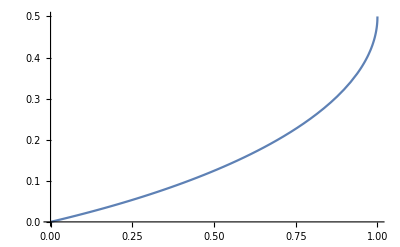

```mathematica
Plot[1/2-1/4(2+(1-3a)y)√(1-y)/.a->0.25,{y,0,1}]
```

```mathematica
FullSimplify[(1/2-1/4(2+(1-3a)y)√(1-y)-xp)(2a+(1-3a)y)/(8 √(1-y))+2(y-yp)]
FullSimplify[%*32 √(1-y)]
```

((a (2-3 y)+y) (2-4 xp+√(1-y) (-2+(-1+3 a) y)))/(32 √(1-y))+2 (y-yp)

(a (2-3 y)+y) (2-4 xp+√(1-y) (-2+(-1+3 a) y))+64 √(1-y) (y-yp)